# Text Analysis with Wikipedia

Examples of natural language processing text processing of a Wikipedia article for a quick summary.

```mathematica
moon=WikipediaData["Moon"];
```

```mathematica
Snippet[moon,5]
```

The Moon is Earth's only natural satellite. It orbits at an average distance of
384400 km (238900 mi), about 30 times the planet's diameter. The Moon always
presents the same side to Earth, because gravitational pull has locked its
rotation to the planet. This results in the lunar day of 29.5 days matching the
lunar month. The Moon's gravitational pull – and to a lesser extent the Sun's –

```mathematica
contents=TextContents[moon,VerifyInterpretation->True];
```

Loading Initialization Data...

Loading Initialization Data...

```mathematica
counts=ReverseSort@CountsBy[contents,Type&]
```

Dataset[Association[AstronomicalObject→463,PlanetaryMoon→392,PhysicalConstant→389,Quantity→197,Unit→161,Planet→158,Date→133,Year→121,Star→69,OrdinalNumber→56,TopologicalSpaceType→42,Country→40,Mythology→34,Color→32,GovernmentAgency→32,Language→30,GeologicalLayer→27,Time→24,Person→23,GivenName→21,Nationality→17,Organization→16,Occupation→16,Element→16,DeepSpaceProbe→14,HistoricalCountry→13,NonperiodicTiling→13,MannedSpaceMission→12,Food→10,SolarSystemFeature→9,Surname→8,Religion→7,Species→7,Satellite→7,Mineral→7,Continent→6,MeasurementDevice→5,SportEvent→5,EthnicGroup→5,AstronomicalObjectType→4,FoodManufacturer→4,GeographicRegion→4,MeteorShower→3,MilitaryConflict→2,TimeZone→2,Season→2,Chemical→2,WaterBodyType→2,MusicWork→1,Company→1,Museum→1,Constellation→1,Desert→1,Ocean→1,USState→1,AdministrativeDivision→1,Surface→1,Cave→1],TypeSystem`Assoc[TypeSystem`Atom[String],TypeSystem`Atom[Integer],TypeSystem`AnyLength],Association[]]

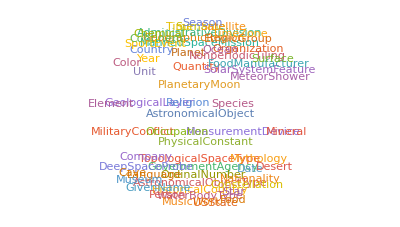

```mathematica
Show[WordCloud[counts],ImageSize->Full]
```

```mathematica
Normal[Select[contents,Type==="Person"&][[All,"String"]]]
```

{Anaxagoras,Aristotle,Archimedes,Seleucus of Seleucia,Ptolemy,Aryabhata,Alhazen,Galileo Galilei,Thomas Harriot,Giovanni Battista Riccioli,Francesco Maria Grimaldi,Wilhelm Beer,Johann Heinrich Mädler,Galileo,Richard Proctor,Grove Karl Gilbert,President John F. Kennedy,Neil Armstrong,Alice Gorman,Virgin Mary,Muhammad,Aristotle,Pliny the Elder}

```mathematica
persons=Normal[Select[contents,Type==="Person"&][[All,"Interpretation"]]]
```

{Anaxagoras,Aristotle,Archimedes,Seleucus of Seleucia,Ptolemy,Aryabhata,Alhazen,Galileo Galilei,Thomas Harriot,Giovanni Riccioli,Francesco Maria Grimaldi,Wilhelm Beer,Johann Heinrich von Mädler,Galileo Galilei,Richard Anthony Proctor,Grove Karl Gilbert,John F. Kennedy,Neil Armstrong,Alice Gorman,Virgin Mary,Muhammad,Aristotle,Pliny the Elder}

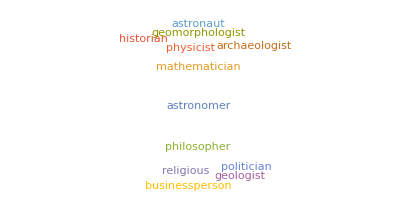

```mathematica
WordCloud[Counts[Flatten@EntityValue[persons,EntityProperty["Person","Occupation"]]]]
```